```mathematica
sanityCheck[]
```

Testing N1440

Testing N1520

Testing N1535

Testing N1650

Testing N1675

Testing N1680

Testing N1700

Testing N1710

Testing N1720

Testing N1900

Testing N1990

Testing N2080

Testing N2190

Testing N2220

Testing N2250

Testing D1232

Testing D1600

Testing D1620

Testing D1700

Testing D1900

Testing D1905

Testing D1910

Testing D1920

Testing D1930

Testing D1950

{True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True}

```mathematica
(* Common *)
comment[c_,val_]:=(Print[c]; val);
atNotebook[path_]:=FileNameJoin[{NotebookDirectory[],path}];
Second[xs_]:=xs[[2]];

sanityCheck[]:=
Map[Block[{h=#},
On[Assert];
Print["Testing "<>ToString[h]];
Assert[m0[h]≥0,"Negative mass"];
Assert[Γ0[h]≥0,"Negative width"];
Assert[Sum[dec[[2]],{dec,decays[h]}]==1.,"Incomplete branching ratios for "<>ToString[h]];
Map[Module[{j1,j2,jOut,lChan,inRange,outRange},
j1=j@#[[1,1]];j2=j@#[[1,2]];jOut=j@h;lChan=#[[3]];
inRange=Range[Abs[j1-j2],Abs[j1+j2]];
outRange=Range[Abs[jOut-lChan],Abs[jOut+lChan]];
Assert[IntersectingQ[inRange,outRange],"Angular momenta inaccessible for "<>ToString[h]<>"-->"<>ToString[#[[1]]]];
]&,decays[h]];
True
]&,Join[Ns,Ds]];


(* Kinematic and helper functions *)
ClearAll[BR]; ClearAll[massDecayBound];
getDecay[hIn_,hOuts_]:=SelectFirst[decays[hIn],#[[1]]==hOuts&];
BR[hIn_,hOuts_]:=getDecay[hIn,hOuts][[2]];
decayAngularMomentum[hIn_,hOuts_]:=getDecay[hIn,hOuts][[3]];
decayProducts[particle_]:=First/@decays[particle];
minMass[particle_]:=If[Γ0[particle]==0.,m0[particle],0.];
massDecayBound[particle_]:=massDecayBound[particle]=
Min[(Total[minMass/@First[#]]&) /@ decays[particle]];

pCMS[eCM_,mA_,mB_]:=If[eCM≤mA+mB,0,1/(2.eCM)*Sqrt[(eCM^2-(mA+mB)^2)(eCM^2-(mA-mB)^2)]];

psSize[mDistribution_][eCM_,{hA_,hB_},lFac_:0]:=Module[{m0A,m0B},
m0A=m0[hA];m0B=m0[hB];
If[Γ0[hA]==Γ0[hB]==0.,
If[eCM<m0A+m0B,Return[0],Return@(pCMS[eCM,m0A,m0B]^lFac)]
];
If[Γ0[hA]==0.,
If[eCM<m0A,Return[0],
Return@NIntegrate[pCMS[eCM,m0A,mB]^lFac mDistribution[hB,mB],{mB,massDecayBound[hB],eCM-m0A}, PrecisionGoal->3,AccuracyGoal->10]
]];
If[Γ0[hB]==0.,
If[eCM<m0B,Return[0],
Return@NIntegrate[pCMS[eCM,mA,m0B]^lFac mDistribution[hA,mA],{mA,massDecayBound[hA],eCM-m0B}, PrecisionGoal->3,AccuracyGoal->10]
]];
NIntegrate[pCMS[eCM,mA,mB]^lFac mDistribution[hA,mA]mDistribution[hB,mB],{mA,massDecayBound[hA],eCM},{mB,massDecayBound[hB],eCM-mA}, PrecisionGoal->3,AccuracyGoal->10]
];

ClearAll[a0];
breitWigner[Γ0_Real,dm_Real]:=Γ0/(dm^2+0.25Γ0^2)
a0[particle_,m_Real]:=If[Γ0[particle]==0.,Throw["In a0: Singular mass distribution for "<>ToString[particle]],
breitWigner[Γ0[particle],m0[particle]-m]/(2Pi)
];
p0Mean=psSize[a0];
ClearAll[p0MeanCh];
p0MeanCh[m0_,{hA_,hB_},lFac_]:=p0MeanCh[m0,{hA,hB},lFac]=p0Mean[m0,{hA,hB},lFac];

ClearAll[Γ];
Γ[hIn_,hOuts_,m_Real]:= Module[{p0,p0res,p01,p0res1,lChan},
If[m≤Sum[minMass[h],{h,hOuts}],Return[0]];
lChan=decayAngularMomentum[hIn,hOuts];

p01=p0Mean[m,hOuts,2lChan+1];
p0res1= p0MeanCh[m0[hIn],hOuts,2lChan+1];
p0=p0Mean[m,hOuts,2lChan]; 
p0res=p0MeanCh[m0[hIn],hOuts,2lChan];

(*
p01=p0Mean[m,hOuts,1]^(2lChan+1);
p0res1= p0MeanCh[m0[hIn],hOuts,1]^(2lChan+1);
p0=If[lChan>0,p0Mean[m,hOuts,1]^(2lChan),1];
p0res=If[lChan>0,p0MeanCh[m0[hIn],hOuts,1]^(2lChan),1];
*)
Assert[p0res>0 && p0res1>0];
Γ0[hIn] BR[hIn,hOuts]* m0[hIn]/m * (p01/p0res1) * 1.2/(1. + 0.2(p0/p0res))
];
Γ[h_,m_]:=Sum[Γ[h,decs,m],{decs,decayProducts[h]}];


(* Define the mass distribution function and <p> *)
ClearAll[aN]; ClearAll[a];
aN[particle_]:=comment["Calculating aN for "<>ToString[particle],
aN[particle]=Re@NIntegrate[breitWigner[Γ[particle,m],m0[particle]-m],{m,massDecayBound[particle],Infinity}]
];

a[particle_,m_Real]:=If[Γ0[particle]==0.,Throw["In a: Singular mass distribution for "<>ToString[particle]],
breitWigner[Γ[particle,m],m0[particle]-m]/aN[particle]
];
pMean=psSize[a];

pLab[mA_,mB_,eCM_]:=If[eCM≤mA+mB,0,Sqrt[(eCM^2-mA^2-mB^2)^2/(4mB^2) - mA^2]];
```

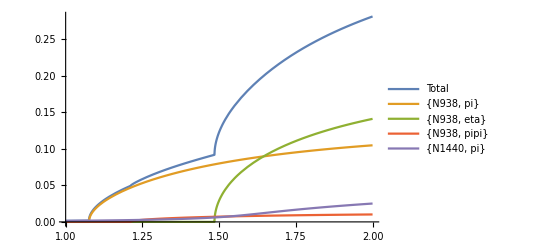

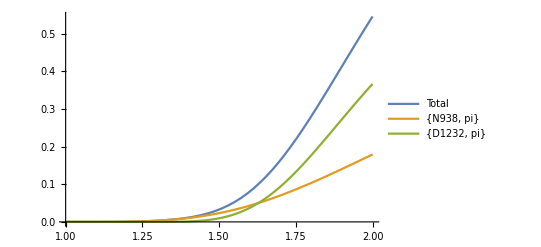

```mathematica
Block[{h=N1535},
Plot[Evaluate@Flatten@{
Γ[h,m],
Table[Γ[h,outs,m],{outs,decayProducts[h]}]
},{m,1.,2.},PlotLegends->Flatten@{"Total",ToString/@decayProducts[h]}]
]
```